# Similarity index

The goal of this research is to find an index that indicates the difference between two rules. In the Game of Life we have the Life rule, but there is also a set of rules called life-like rules, that is, rules that have similar behavior — but how similar? What criteria do we need to consider to say that two rules are similar? If we visualize the evolutions from random initial configurations, these rules appear indistinguishable, since it is only small patterns that alter this behavior. This is why this research seeks to measure the similarity that exists between different rules based on their behavior.

This research is focused primarily on rules in a single dimension.

## Inheritance properties and knew relations

Rule 0 in any cellular automaton is always the same: it does not matter what the neighbors are, it does not matter the number of states, it does not matter the dimensionality — it will always turn all cells to state 0. However, this behavior is not exclusive to rule 0.
For example, the highest rule in any configuration also turns all cells to the highest state regardless of the neighbors. The first task is to find those relations that are exact, i.e., rules that show exactly the same behavior.

Let's start with the simplest configurations, a dimensionless cellular automaton. This CA's only neighbor is itself, since it could be thought of as a machine that evolves and whose only knowledge is its previous state. If we consider only 2 states, then we have the same behavior as a flip-flop, but we can take this a bit further and say that it has only one state; this way we get rule , which is the first rule to exist, with the smallest possible definition, and the only one belonging to that space:

```mathematica
RulePlot[CellularAutomaton[{0,1,0}],ImageSize->100,PlotLegends->Placed[Subscript[0,2,1], Below]]
```

-Graphics-

Now we can make 3 changes to the cellular automaton space: increase the number of states, the number of neighbors, and the dimensionality. Let's start by increasing the number of states:

For 2 states, we can generate the following  rules:

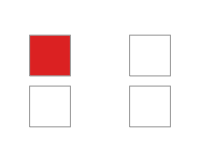
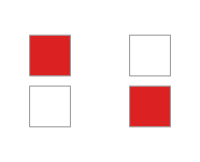
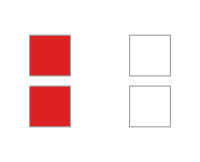
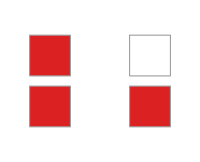
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{RulePlot[CellularAutomaton[{#,2,0}],ColorRules->colorRules[1],ImageSize->200,PlotLegends->Placed[Subscript[#,2,1], Below]]&/@Range[0,3,1]}]
```

As already mentioned, among these rules there are some that have the same behavior, which we can identify as a state permutation. That is, if we have 2 cellular automata whose states are {a,b} and {c,d}, and there exists a function that maps {a,b} -> {c,d} such that all relations in the transition function are preserved, we can say that these rules are identical.

For this case, if we perform the following rule mappings: {0, 1} -> {a,b} and {1,0} -> {b,a}, we find that rule  and  are equivalent. We can visualize this as if we simply swapped the colors:

```mathematica
Grid[{RulePlot[CellularAutomaton[{#,2,0}],ColorRules->colorRules[1],ImageSize->100,PlotLegends->Placed[Subscript[#,2,1], Below]]&/@{0,3},
RulePlot[CellularAutomaton[{#,2,0}],ColorRules->{1->RGBColor[1., 1., 1.],0->RGBColor[0.857359, 0.131106, 0.132128]},ImageSize->100,PlotLegends->Placed[Subscript[#,2,1], Below]]&/@{0,3}}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

State permutation is not unique to 2 states; in that case it is simple because it is just swapping one for the other. When we have more states, state permutation tells us to map all states through every possible permutation. This is the case for 3 states:

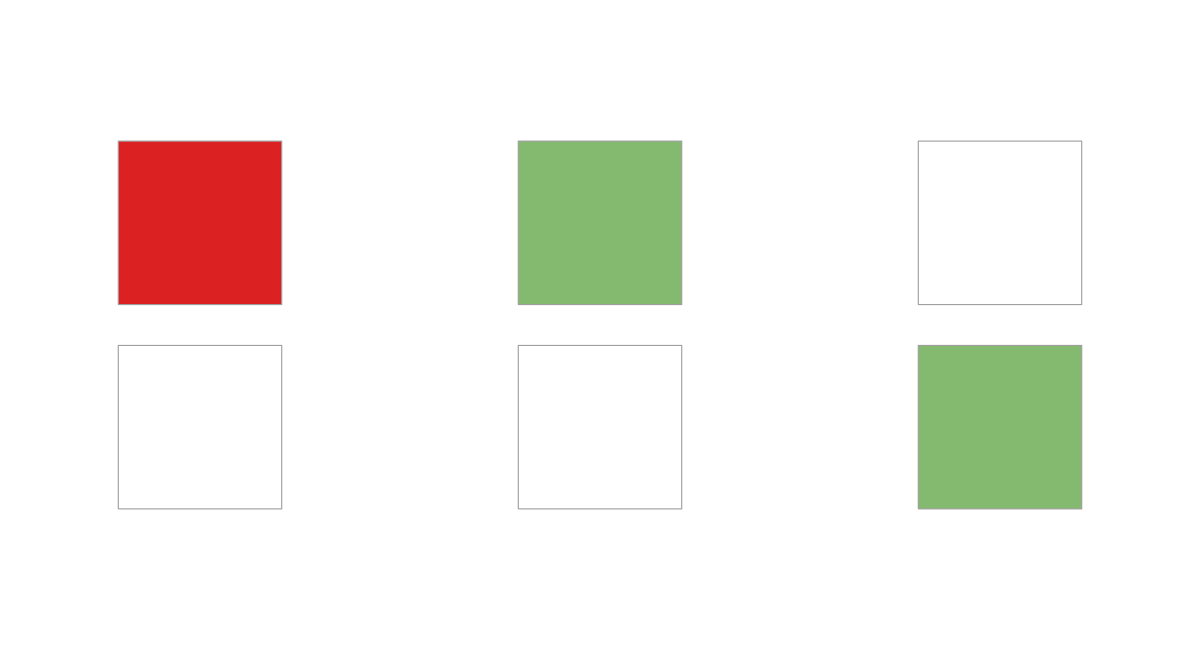
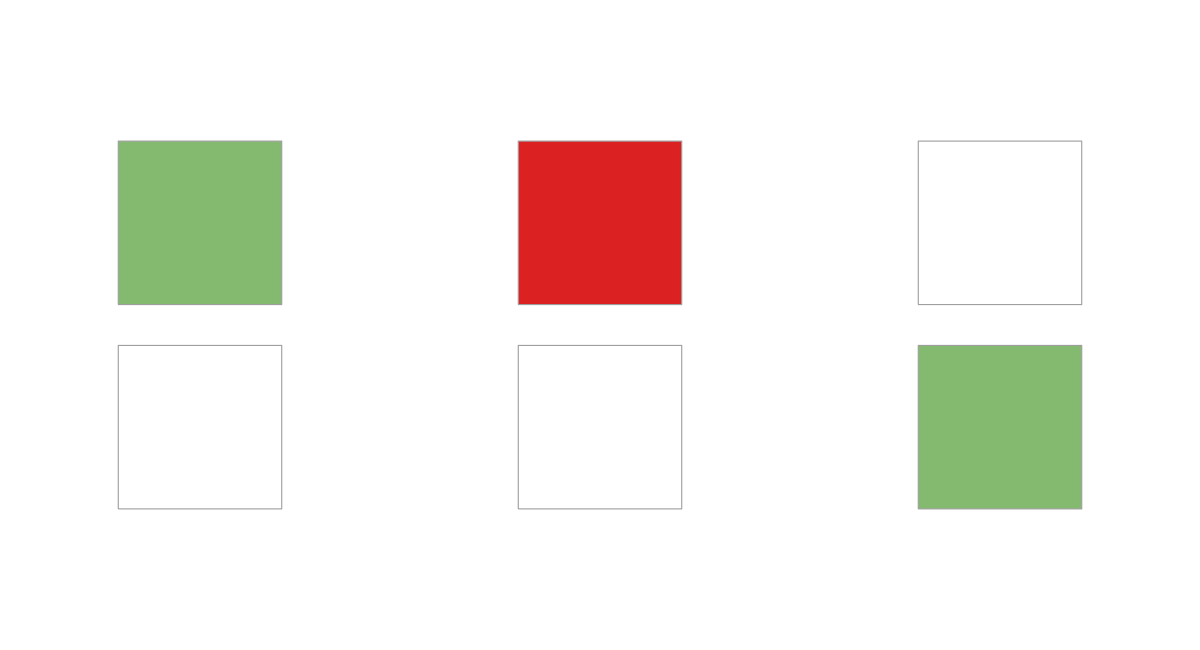
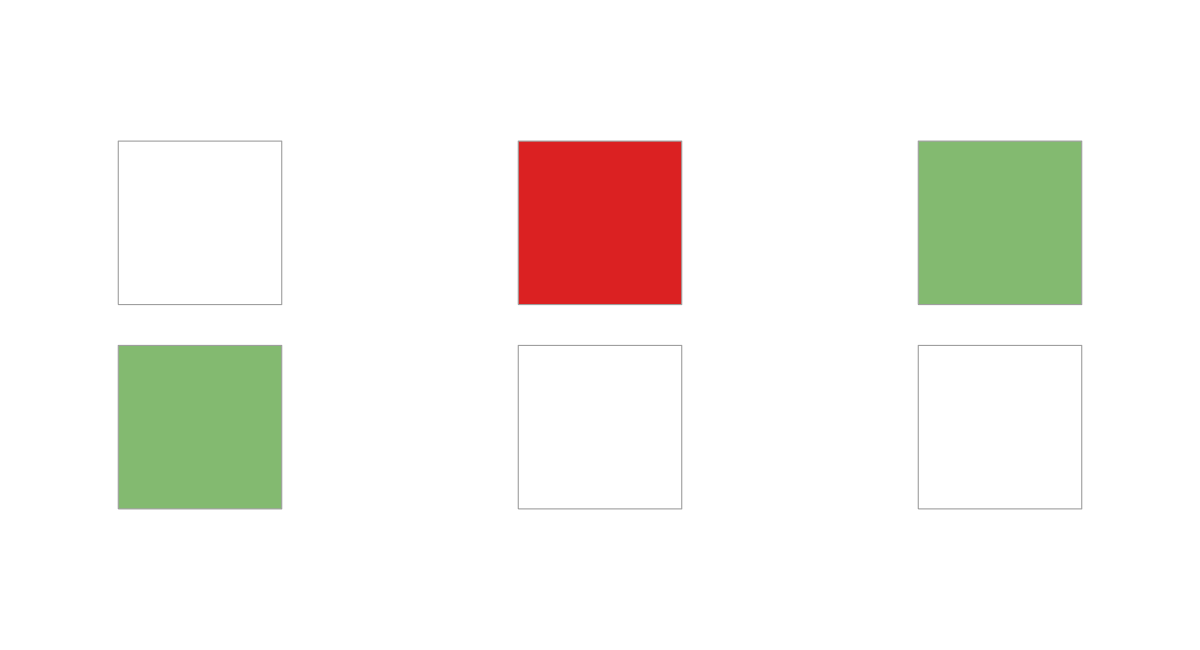
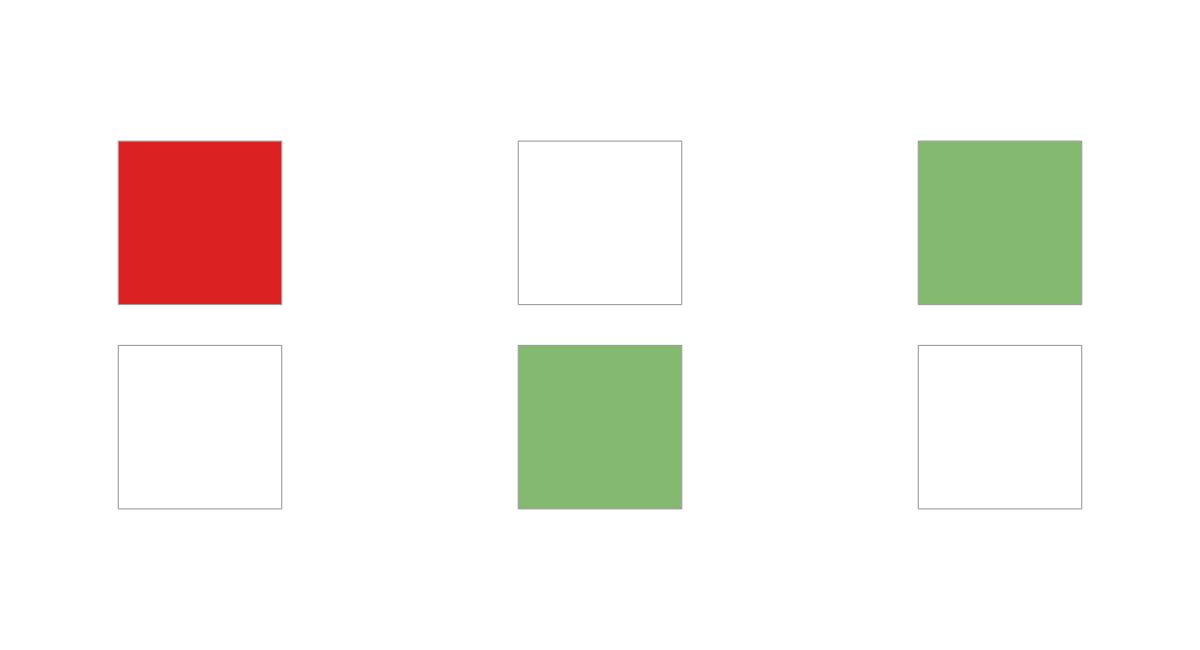
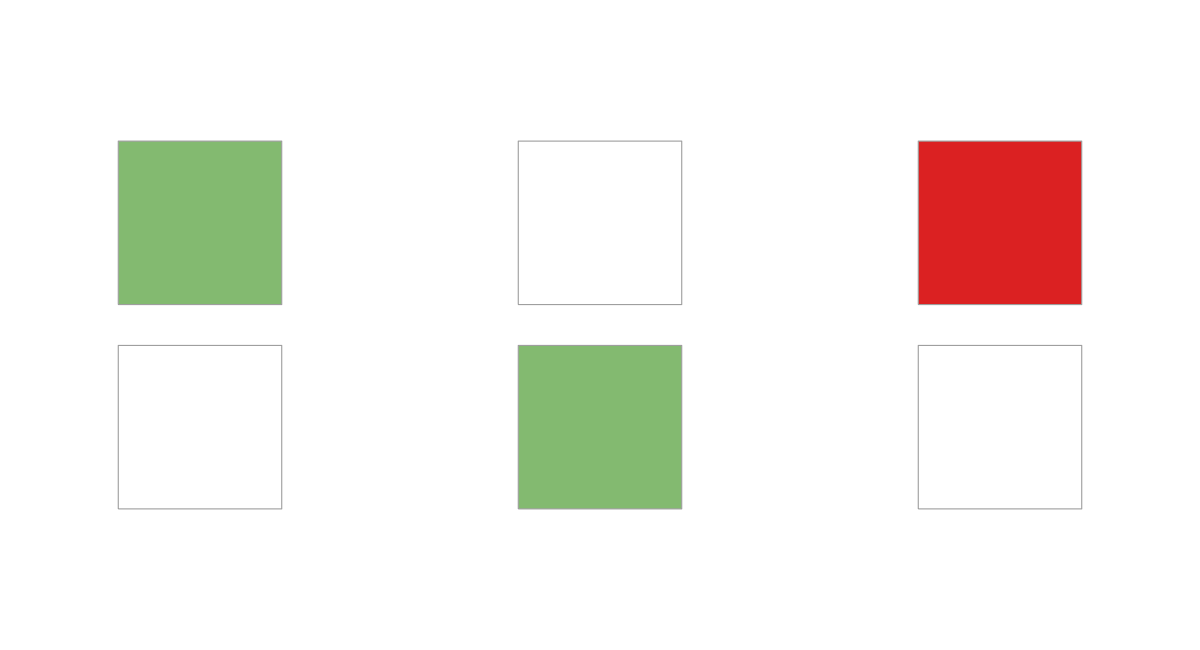
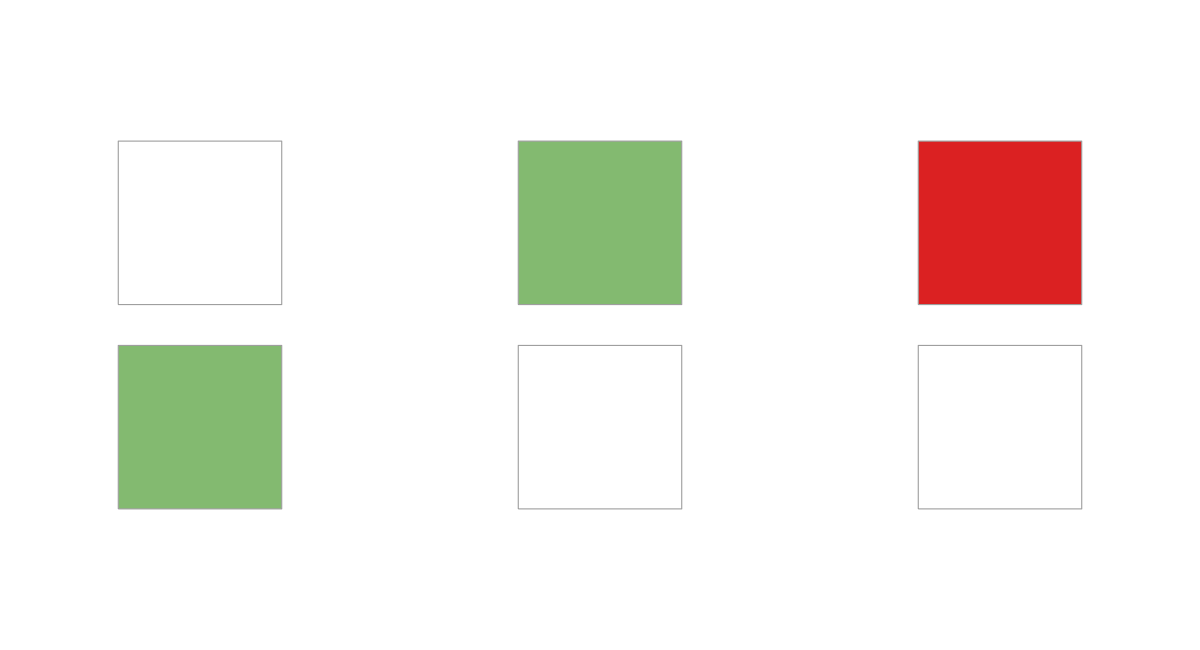
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
crs={{0->RGBColor[1., 1., 1.],1->RGBColor[0.513417, 0.72992, 0.440682],2->RGBColor[0.857359, 0.131106, 0.132128]},{0->RGBColor[1., 1., 1.],2->RGBColor[0.513417, 0.72992, 0.440682],1->RGBColor[0.857359, 0.131106, 0.132128]},{2->RGBColor[1., 1., 1.],0->RGBColor[0.513417, 0.72992, 0.440682],1->RGBColor[0.857359, 0.131106, 0.132128]},{1->RGBColor[1., 1., 1.],0->RGBColor[0.513417, 0.72992, 0.440682],2->RGBColor[0.857359, 0.131106, 0.132128]},{1->RGBColor[1., 1., 1.],2->RGBColor[0.513417, 0.72992, 0.440682],0->RGBColor[0.857359, 0.131106, 0.132128]},{2->RGBColor[1., 1., 1.],1->RGBColor[0.513417, 0.72992, 0.440682],0->RGBColor[0.857359, 0.131106, 0.132128]}};
Grid[Partition[Labeled[CaRulePlot[#[[1]],ColorRules->#[[2]]],#[[1]]]&/@Transpose[{InverseRules[],crs}],3]]
```

If we consider that all these rules have the same behavior, then the number of behaviors is smaller than the number of rules; we can see how the total number of behaviors drops drastically as the number of states increases.

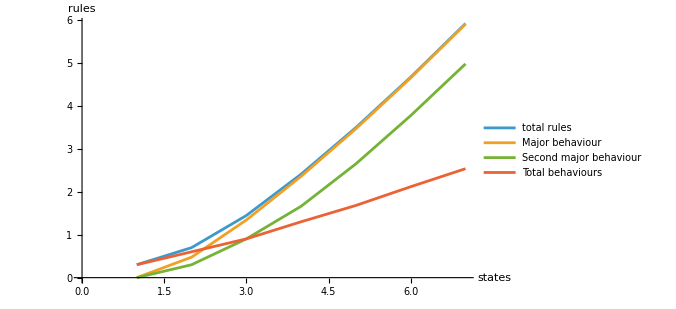

```mathematica
urs=;
ListLinePlot[
Transpose[MapThread[{#1^#1,#2[[-1,1]],If[Length[#2]>=2,#2[[-2,1]],0],Length[#2]}&,{Range[7],urs}]],
ScalingFunctions->"SignedLog",
PlotLegends->{"total rules","Major behaviour","Second major behaviour","Total behaviours"},
ImageSize->500,
AxesLabel->{"states", "rules"}
]
```

The following plot shows the rule vectors of the unique behaviors. We can observe that the rules with  states are a subset of the rules with  states where the new state has a transition to 0

```mathematica
burs=Table[IntegerDigits[#,Max[2,i],i]&/@urs[[i,;;,1]],{i,1,Length[urs]}];
Module[{cell=10,maxRows=50},
Grid[{With[{nrows=Min[maxRows,Dimensions[#][[1]]],
ncols=Dimensions[#][[2]]},
ArrayPlot[#[[;;UpTo[maxRows]]],
ColorRules->colorRules[5],
Mesh->True,
MeshStyle->Directive[GrayLevel[0.4],AbsoluteThickness[0.75]],
PlotRangePadding->0,
ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},
ImageSize->{cell*ncols,cell*maxRows}]]&/@burs
},Spacings->{2, 0}]
]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

The next hypothesis was that there exists a mapping between rules that allows us to move between CA spaces. That is, we can move from rule  to  simply by adding a new state that points to state 0. Consider the following examples, where the pattern is shown to be exactly the same no matter how many states we add

Rules {0,0,0,0,0,0,0}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],3]&/@Select[urv,#["vector"]=={0,0,0,0,0,0,0}&][[2;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules[6],Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Rules {0,0,0,0,0,0,1}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],3]&/@Select[urv,#["vector"]=={0,0,0,0,0,0,1}&][[2;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules[6],Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Rules {0,0,0,0,1,1,2}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],3]&/@Select[urv,#["vector"]=={0,0,0,0,1,1,2}&][[;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules[6],Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-

Rules {0,0,0,0,1,1,1}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],3]&/@Select[urv,#["vector"]=={0,0,0,0,1,1,1}&][[;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules[6],Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics-

We can carry out the reverse process and remove states. For this, 2 conditions must be satisfied:

The last state must transition to 0

No state may transition to the last state

However, when trying to apply this reduction we find that it fails for some rules, for example :

```mathematica
Grid[{Module[{cas={CellularAutomaton[{31,5,0},Range[4,0,-1],5],CellularAutomaton[{21,4,0},Range[3,0,-1],5],CellularAutomaton[{13,3,0},Range[2,0,-1],5]},labels={Subscript[31,5,1],Subscript[21,4,1],Subscript[13,3,1]},cell=30},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},MapThread[With[{nrows=Dimensions[#1][[1]],ncols=Dimensions[#1][[2]]},ArrayPlot[#1,ColorRules->colorRules[4],Mesh->True,PlotRangePadding->0,PlotLabel->#2,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&,{cas,labels}]]]}]
```

-Graphics-

since neither rule  nor  belongs to the list of unique behaviors. But we can find the similarity through state permutation and navigate the connection graph, as shown below:

```mathematica
Module[{
vectors={{0,0,1,1,1},{0,1,1,1},{1,1,1},{0,0,0},{0,0},{0},{0,0,2,0},{0,2,0},{0,1,1},{1,1}},
edges={{0,0,1,1,1}->{0,1,1,1},{0,1,1,1}->{1,1,1},{1,1,1}->{0,0,0},{0,0,0}->{0,0},{0,0}->{0},{0,1,1,1}->{0,0,2,0},{0,0,2,0}->{0,2,0},{0,2,0}->{0,1,1},{0,1,1}->{1,1},{1,1}->{0,0}},
colores={({0,0,1,1,1}->{0,1,1,1})->Red,({1,1}->{0,0})->Blue,({0,1,1,1}->{1,1,1})->Red,({0,0,0}->{0,0})->Red,({0,0}->{0})->Red,({0,0,2,0}->{0,2,0})->Red,({0,1,1}->{1,1})->Red,({1,1,1}->{0,0,0})->Blue,({0,1,1,1}->{0,0,2,0})->Blue,({0,2,0}->{0,1,1})->Blue}},
Legended[LayeredGraph[
Graph[
edges,
EdgeStyle->colores,
VertexShapeFunction->(Inset[
ArrayPlot[{#2},
ColorRules->colorRules[2],
ImageSize->{Length[#2]*20,20},
Mesh->True,
MeshStyle->Gray,
ImagePadding->0,
PlotRangePadding->0
],#1]&),
VertexSize->{0.01,0.25}],
ImageSize->{450,Automatic}
],LineLegend[colores[[All,2]],{"Delete last state","Minor inverse rule"}]]
]
```

-Graphics-

With these 2 types of relations we can define the following connections, where each level represents the number of states, each label represents the representative rule of each unique behavior, and each arrow is a state reduction. It is no surprise that most of the connections point toward rule , keeping in mind that this is only for dimensionless CAs.

The next step is to increase the dimensionality and, therefore, the number of neighbors, starting with two neighbors and 2 states. We can again apply the state-permutation reduction, giving us the following rules

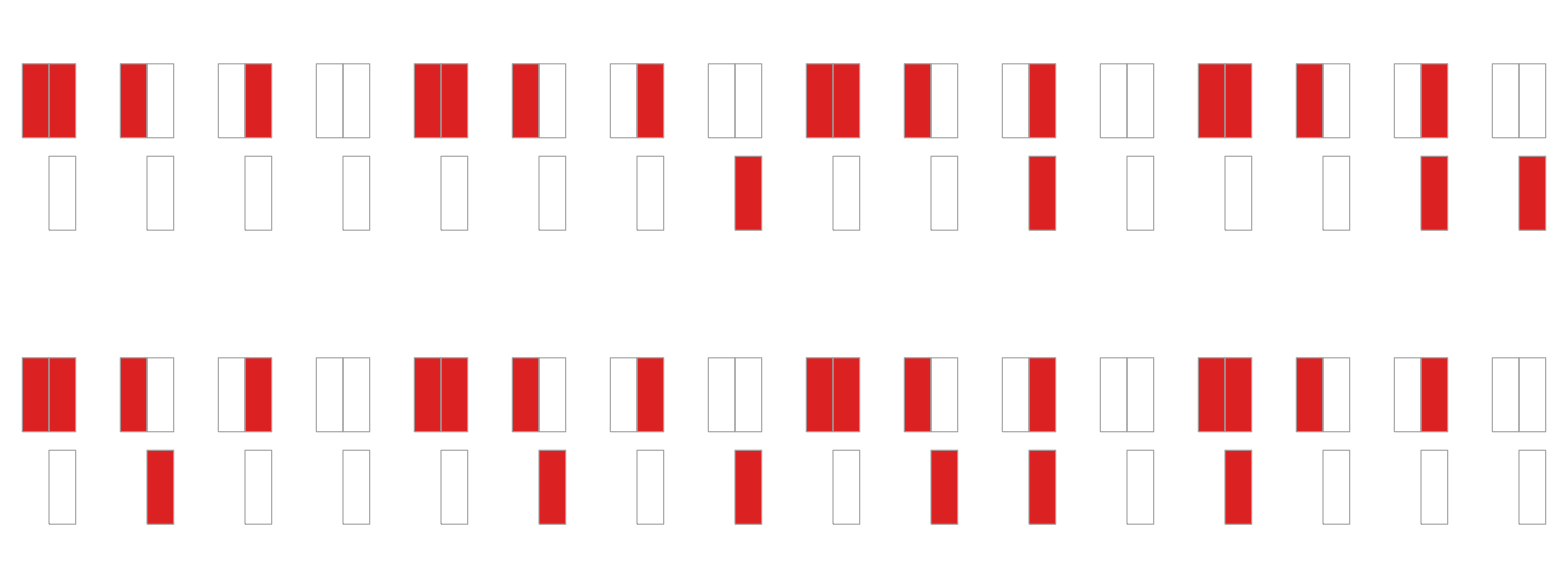

```mathematica
assoc=#[[1]]->#&/@DeleteDuplicates[InverseRules[Subscript@@{#,2,2}]&/@Range[0,15]];
Grid[Partition[CaRulePlot[Subscript@@#[[1]]]&/@assoc,4]]
```

Now we find another behavioral similarity: rules for which, if we reverse the evolution, we obtain the same behavior. This is the case for the following 2 rules:

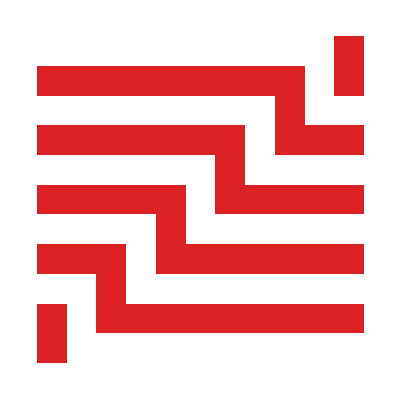
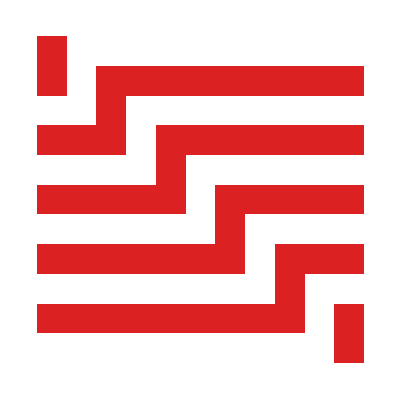
-Graphics- | -Graphics-

```mathematica
init={{1},0};
Grid[{{
RulePlot[CellularAutomaton[{3,2,ReverseSort[{{0},{1}}]}],init,10,PlotLegends->"Text",ColorRules->colorRules[1]],
RulePlot[CellularAutomaton[{5,2,ReverseSort[{{0},{-1}}]}],init,10,PlotLegends->"Text",ColorRules->colorRules[1]]}
}]
```

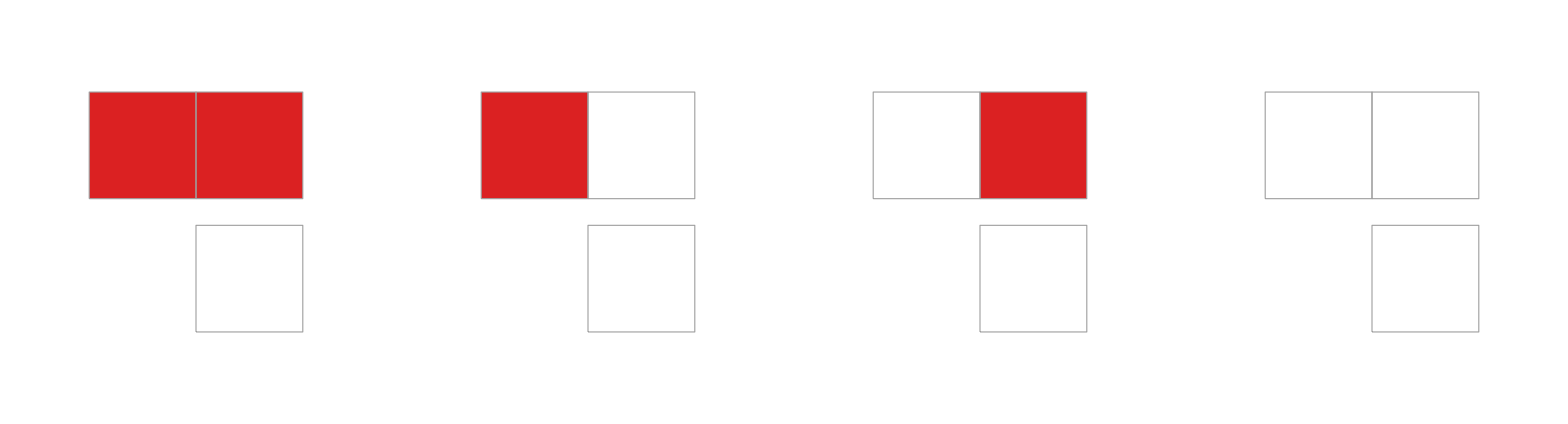
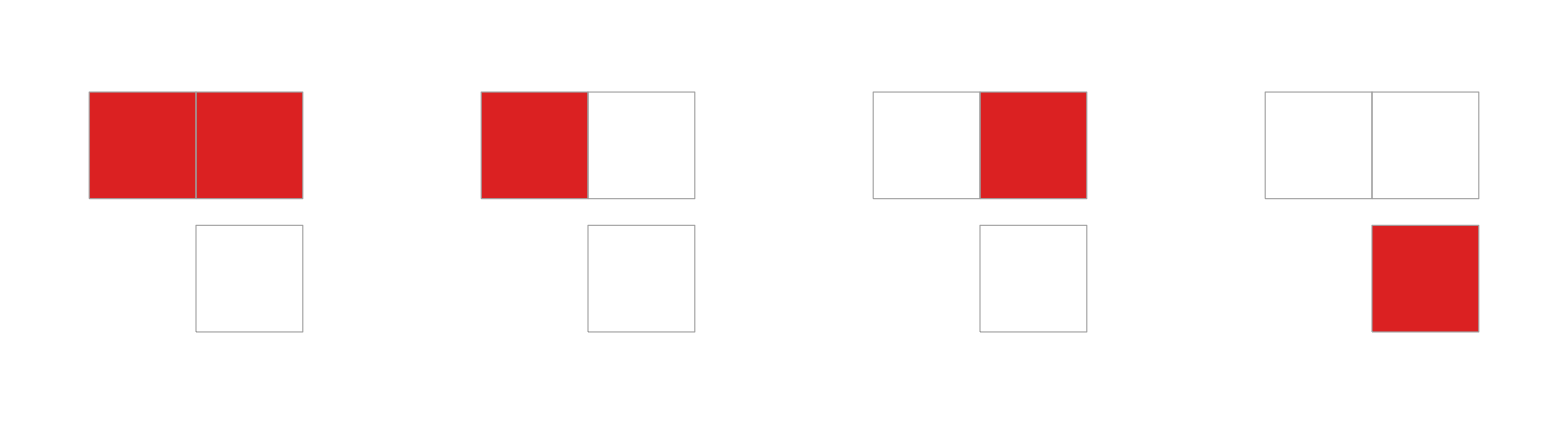
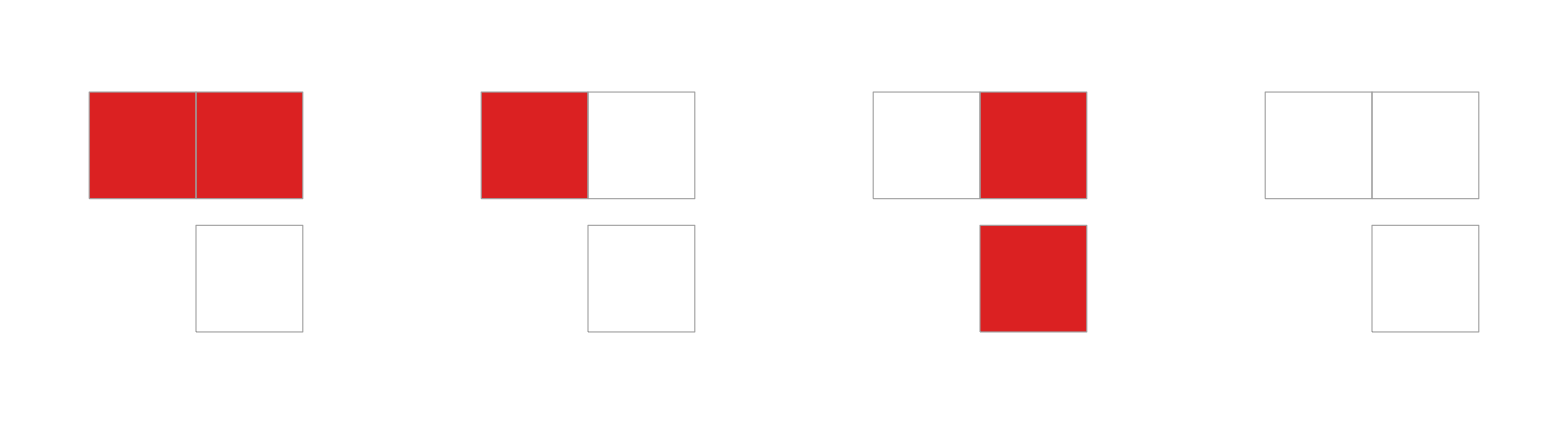
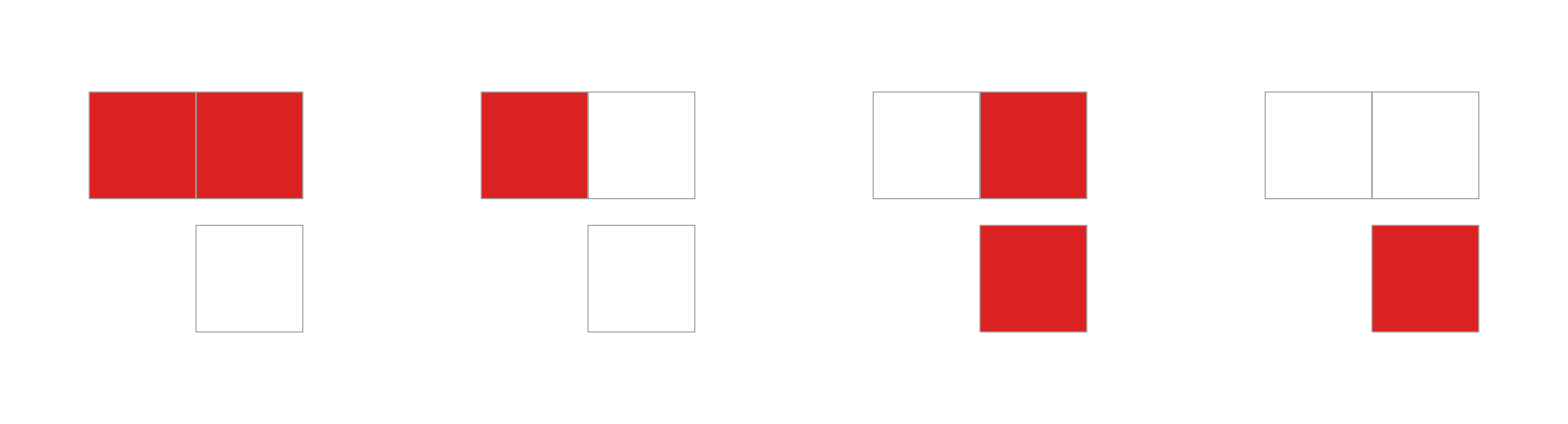
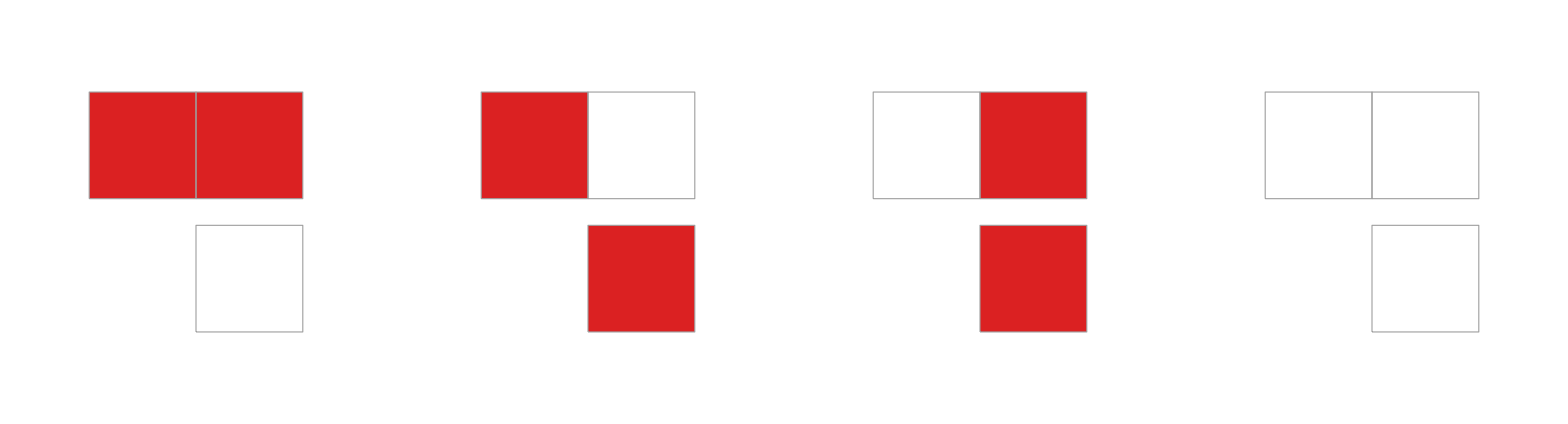
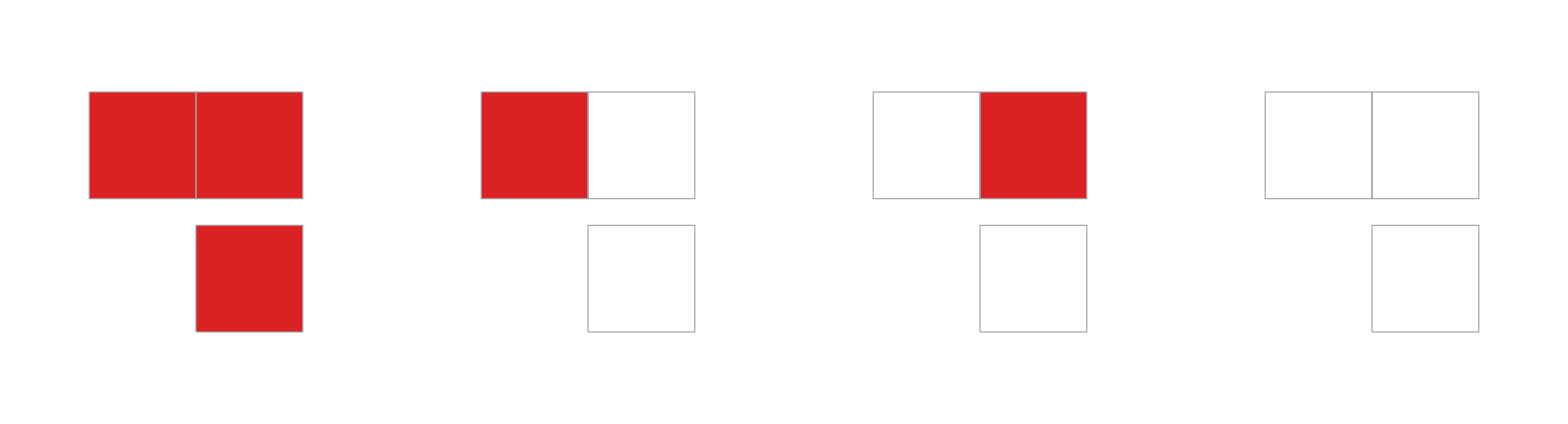
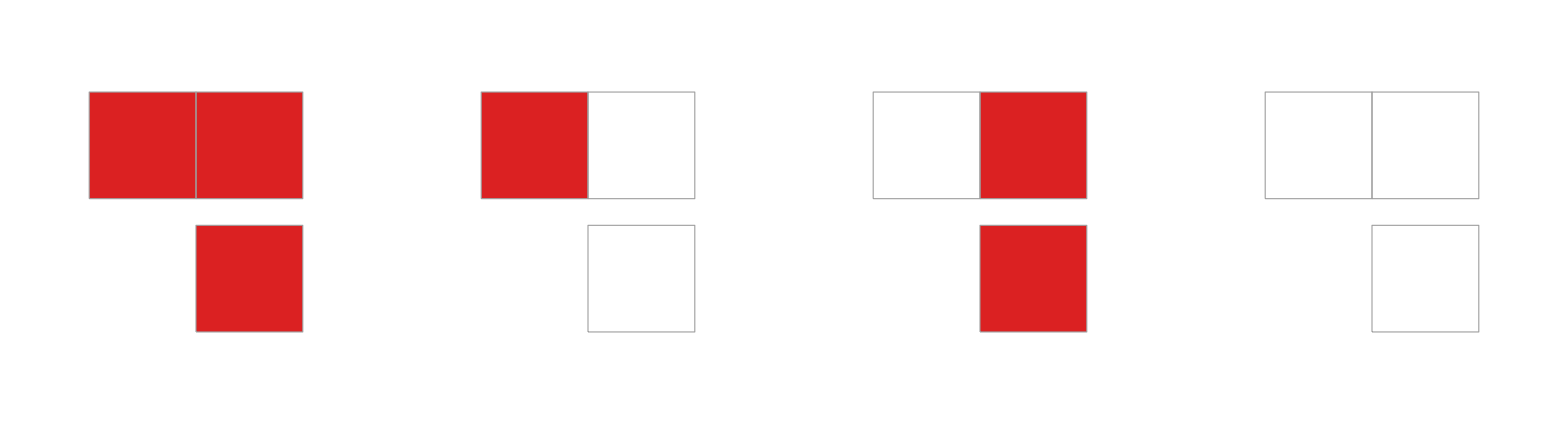
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Grid[Partition[CaRulePlot[Subscript@@{#,2,2}]&/@{0,1,2,3,6,8,10},UpTo[4]]]
```

From these behaviors, we find 3 relations with previous configurations.

Rule  does not depend on either one, just like  and

Rule  depends only on the left neighbor, so it mimics rule

Rule  depends only on the right neighbor, so it mimics rule

```mathematica
Grid[{{rulialGraph[{{0,2,1/2}->{0,1,1/2},{0,1,1/2}->{0,1,0},{0,2,1/2}->{0,2,0},{0,2,0}->{0,1,0}},Red],
rulialGraph[{{3,2,1/2}->{1,2,0}},Red],
rulialGraph[{{10,2,1/2}->{2,2,0}},Red]}}]
```

-Graphics-

The evolutions of rules  and  are exactly the same. For rule  and  we need to consider that it is the inverse of the cell to the left, so if we shift the blocks to the left, we find the same behavior.

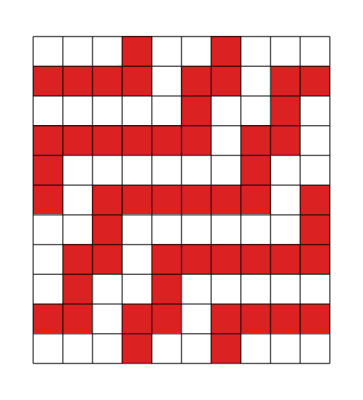
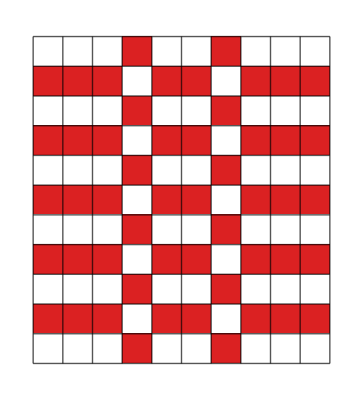
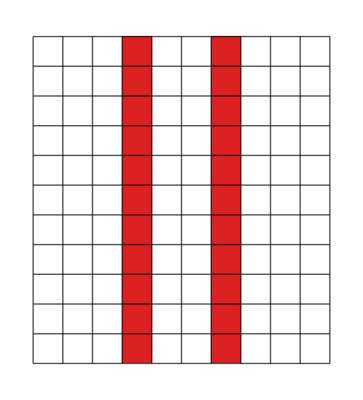
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
init={0,0,0,1,0,0,1,0,0,0};
Grid[{RulePlot[CellularAutomaton[#],init,10,PlotLegends->"Icon",ColorRules->colorRules[1],Mesh->True]&/@{{3,2,1/2},{1,2,0},{10,2,1/2},{2,2,0}}
}]
```

In the end, we have only 4 unique behaviors:

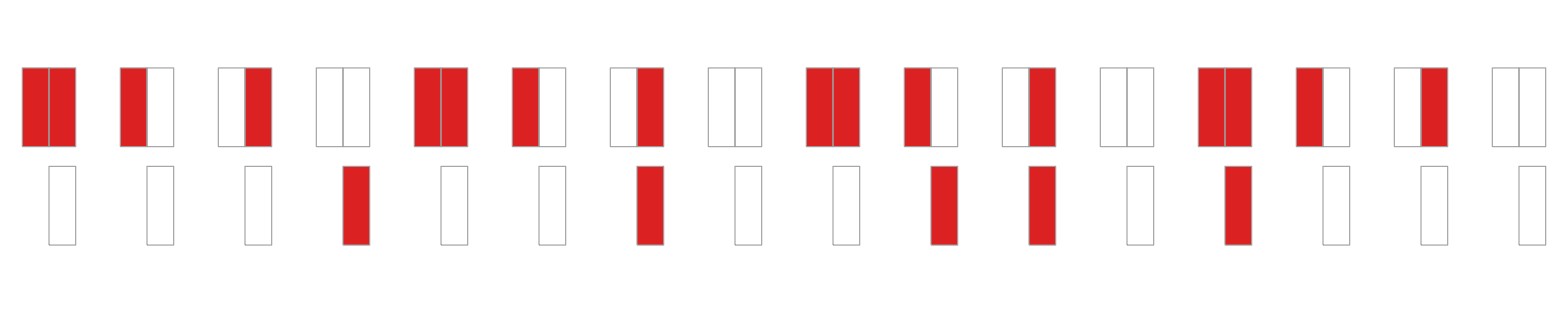

```mathematica
Grid[{CaRulePlot[Subscript@@{#,2,2}]&/@{1,2,6,8}}]
```

With random seeds, we find the following behaviors; none of them are reversible.

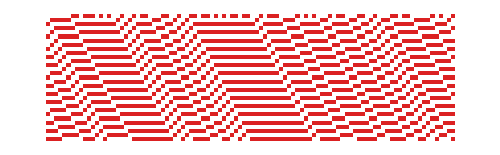
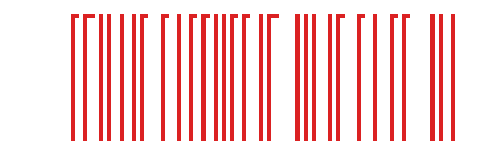
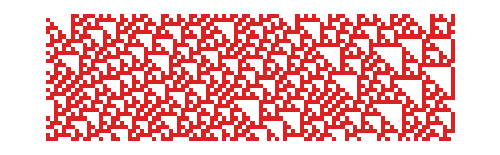
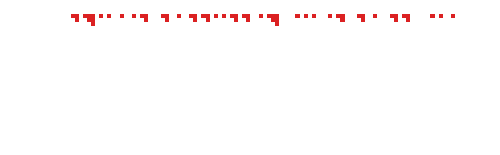
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
init=RandomInteger[{0,1},100];
Grid[Partition[RulePlot[CellularAutomaton[{#,2,1/2}],init,30,ColorRules->colorRules[1],ImageSize->500,PlotLegends->"Icon"]&/@{1,2,6,8},2]]
```

The similarity functions tell us that 2 rules have the same behavior within the same space. Inheritance rules mean that they are rules whose behavior can be obtained from a rule with either fewer states or fewer neighbors. The last step of this research is dimensionality reduction. It is the most complex step because, up to now, the neighbors have always been grouped together. If we say we have 2 neighbors, we assume those 2 neighbors are the 2 closest neighbors, because seeing this on a line is fairly simple; the problem is trying to see it now in 2 dimensions. By proximity, I can say that the 2 closest neighbors have 2 possibilities:

```mathematica
Grid[{{ArrayPlot[{{0,0,0},{1,2,1},{0,0,0}},ColorRules->colorRules[2],Mesh->True],ArrayPlot[{{0,1,0},{1,2,0},{0,0,0}},ColorRules->colorRules[2],Mesh->True]}}]
```

-Graphics-

And both have completely different behaviors, because even though the number of rules and the rule vector are equivalent: , one of them has a dimensionality reduction because it only considers the elements along one axis — in this case, the first one only considers left and right, regardless of the remaining dimensions. 
Another event that can happen is a neighborhood reduction that is later followed by a dimensionality reduction. 
Additionally, it will be necessary to start specifying the positions of the elements, because, for example, up to now we have assumed that the neighbors are always the closest ones to the center, even if there are only 2 of them, but we have not verified whether this holds for any 2 neighbors we might pick. This is because there are some configurations where it does hold true, but others where it needs to be investigated in depth.

For example, are the following 5 rules the same? We are assuming they are, but the only difference is which neighbors we are taking. So, under the definition we have been using, they are all rule , but their neighbors are in different positions; if we look closely, they seem to have the same behavior, only shifted or remapped, but the behavior appears to be the same for all of them. The Sierpinski triangle belongs to a different rule space.

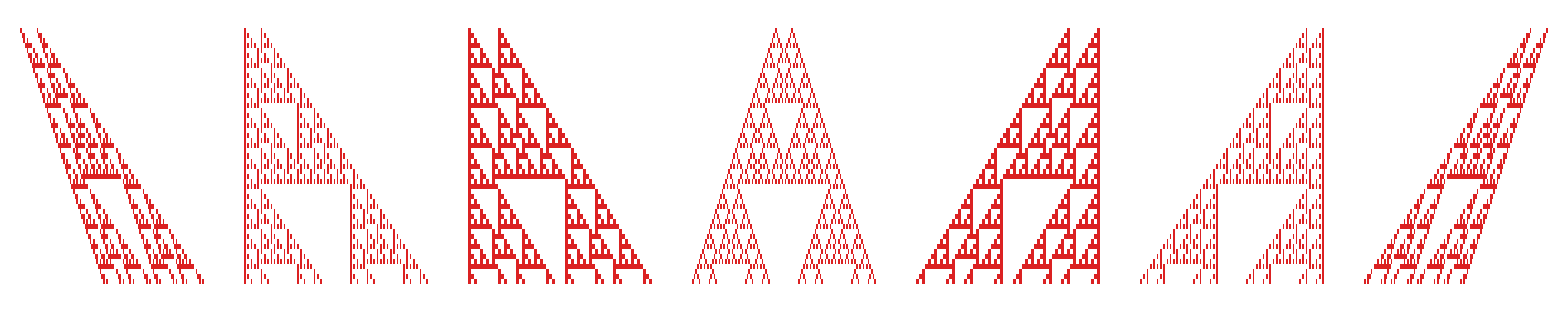

```mathematica
init={{0,0,1,0,0,0,0,0,0,0,0,0,1,0,0},0};
Grid[{{
ArrayPlot[CellularAutomaton[{6,2,{{-2},{-1}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{-2},{0}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{-1},{0}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{-1},{1}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{0},{1}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{2},{0}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{2},{1}}},init,50],ColorRules->colorRules[1]]
}}]
```

With the following preloaded data, we show all the relations discovered for CAs with relatively small configurations:

```mathematica
data=addData[Join[getRules[2,1],getRules[3,1],getRules[2,2],getRules[3,2]]];
```

```mathematica
rdata=reduce[data];
```

However, all the experiments carried out so far only tell us whether 2 rules have the same behavior or not — a binary classification that does not tell us how similar these rules are based on their behaviors. Under this method, we would find that life-like rules are completely different from the Life rule, which is counterintuitive. The next step toward finding the similarity between rules is to compare the evolutions in the evolution graph.

## Evolution graph

For this part, what we will do is evolve a cellular automaton across all possible finite spaces. With this, we will build a transition graph that lets us compare the behavior of their transitions, looking for a similarity between these elements. Let's take as an example rule 0 and rule 255 of an ECA on a space of 5 cells:

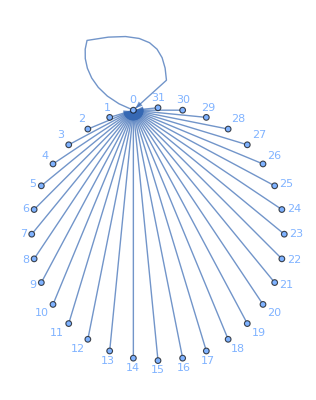
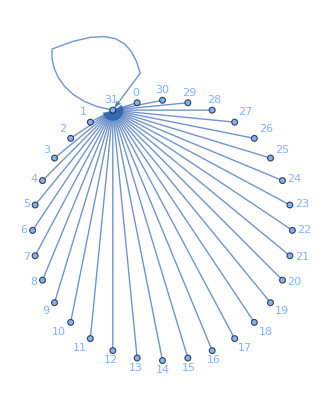
-Graphics-0_(2,3) | -Graphics-255_(2,3)

```mathematica
inits=Tuples[Range[0,1],5];
r255=FromDigits[#[[1]],2]->FromDigits[#[[2]],2]&/@(CaArray[Subscript[255,2,3],#,1]&/@inits);
r0=FromDigits[#[[1]],2]->FromDigits[#[[2]],2]&/@(CaArray[Subscript[0,2,3],#,1]&/@inits);
Grid[{{Labeled[Graph[r0,VertexLabels->Automatic,GraphLayout->"CircularEmbedding"],],Labeled[Graph[r255,VertexLabels->Automatic,GraphLayout->"CircularEmbedding"],]}},Frame->All]
```

Each node is a space represented in its decimal form, and each node has exactly one transition to another configuration. We see that rules  and  have exactly the same shape but differ in their labels. 
We can say that these 2 graphs are isomorphic, that is, there exists a bijective function that can map each vertex in the transition matrix — in this case, swapping 0 for 31

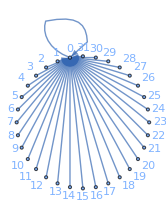
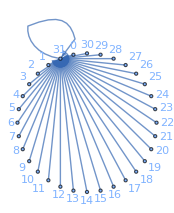
```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

True

One approach is to find the canonical form of the graphs, that is, a way of organizing the graph so as to know only its topology without labeling the relations or nodes. A common way to do this can be by using the eigenvalues as a feature vector, following this process:

We extract the transition matrix

We compute the eigenvalues of the matrix

We compare the 2 vectors using cosine distance.

```mathematica
ev0=Eigenvalues[Normal[AdjacencyMatrix[-Graphics-]]];
ev255=Eigenvalues[Normal[AdjacencyMatrix[-Graphics-]]];
CosineDistance[ev0,ev255]
```

0

If the distance is 0, it means these 2 rules are equivalent. But this is not only useful for identifying whether they are exactly the same (as in the previous method) — this method also tells us how much difference exists between these 2 rules, which in this case is 0.
For example, rule 8 tends to put all configurations to 0 just like rule 0, but taking a larger number of steps.

```mathematica
ss=7;
EigenvaluesGraphDistance[MakeGraph[,ss],MakeGraph[,ss]]
```

0.

```mathematica
CanonFuncGraph[g_Graph]:=Module[{verts,index,f,n,indeg,preds,code,queue,visited,cycles,succ},verts=VertexList[g];n=Length[verts];index=AssociationThread[verts,Range[n]];succ=Association[(#1⟦1⟧->#1⟦2⟧&)/@EdgeList[g]];f=Table[index[succ[v]],{v,verts}];indeg=ConstantArray[0,n];Do[indeg⟦f⟦i⟧⟧++,{i,n}];preds=ConstantArray[{},n];code=ConstantArray[Null,n];queue=Flatten[Position[indeg,0]];While[queue=!={},With[{v=First[queue]},queue=Rest[queue];code⟦v⟧={Sort[preds⟦v⟧]};With[{w=f⟦v⟧},AppendTo[preds⟦w⟧,code⟦v⟧];If[--indeg⟦w⟧==0,AppendTo[queue,w]]]]];visited=ConstantArray[False,n];cycles={};Do[If[indeg⟦v⟧>0&&!visited⟦v⟧,Module[{c={},w=v},While[!visited⟦w⟧,visited⟦w⟧=True;AppendTo[c,w];w=f⟦w⟧];AppendTo[cycles,c]]],{v,n}];Sort[(Module[{seq=({Sort[preds⟦#1⟧]}&)/@#1},First[Sort[Table[RotateLeft[seq,j],{j,Length[seq]}]]]]&)/@cycles]]
```

```mathematica
CanonFuncGraphQ[g1_Graph,g2_Graph]:=CanonFuncGraph[g1]===CanonFuncGraph[g2]
```

With this, we can generate the similarity matrix between all ECA rules.

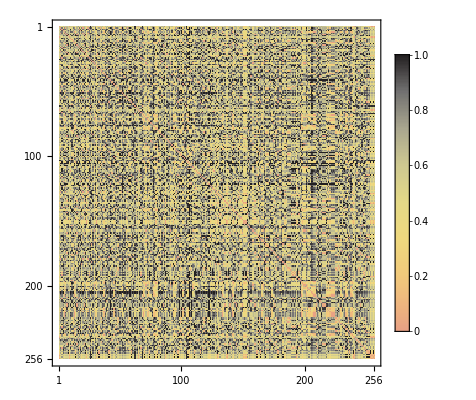

```mathematica
ecaGraphs=ParallelTable[MakeGraph[Subscript[i,2,3],6],{i,0,255,1}];
distances=1-DistanceMatrix[ecaGraphs,DistanceFunction->EigenvaluesGraphDistance];
MatrixPlot[distances,ColorFunction->"CMYKColors",PlotLegends->Automatic]
```

From this procedure, 2 problems arise, which we will try to solve next. With the previous method we could compare rules belonging to different spaces, whether due to a different number of states or a different neighborhood size, but this method is limited since the size of the eigenvalue vector is determined by the number of nodes. Therefore, to compare 2 different spaces, they must have the same number of available spaces, for example:

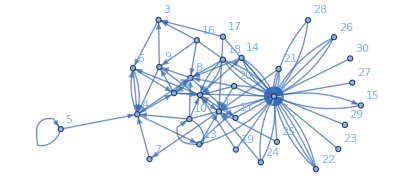
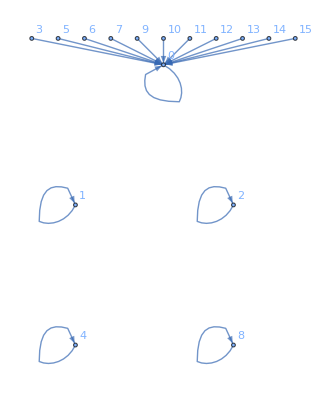
4_(3,2) | 4_(2,4)
-Graphics- | -Graphics-
Total vertex:31 | Total vertex:16
{2.67226,-1.66919,0.436134,0.436134,-1.05038,-1.05038,1.,-1.,1.,1.,-0.174314,-0.174314,-0.275455,-0.275455,0.706521,0.418448,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Grid[Transpose[Module[{g},
Table[
g=MakeGraph[i,4];
{
i,
g,
"Total vertex:"<>ToString[Length[VertexList[g]]],
Re[Eigenvalues[N[Normal[AdjacencyMatrix[g]]]]]
},
{i,{,}}]
]],
Frame->All
]
```

The second problem is to define the space size that best captures the number of unique behaviors that exist. If we increase the space size, we can find more behaviors; the following table shows how the number of unique behaviors increases as we increase the space, but it has a limit or a trend.

```mathematica
ees=Transpose@ParallelTable[
EigenvaluesGraph[MakeGraph[Subscript[r,2,3],ss]],
{r,0,255},{ss,1,8}
];
```

```mathematica
Length[DeleteDuplicates[#]]&/@ees
```

{3,8,24,52,52,68,60,69}

## Rotation-class graph

We test an alternative graph construction: instead of every configuration being a distinct node, we identify configurations that are cyclic rotations of each other (e.g. in a 4-cell space, 0001, 0010, 0100 and 1000 are stored as the same node). This is well defined because CaArray uses a cyclic boundary and the rule is homogeneous: rotating the initial state and evolving gives the same result, rotated, as evolving and then rotating.

```mathematica
RotClass[state_List]:=First[Sort[NestList[RotateLeft,state,Length[state]-1]]]
```

```mathematica
MakeGraphRot[ca_Subscript,spaceSize_]:=Module[{classes},classes=DeleteDuplicates[RotClass/@Tuples[Range[0,ca⟦2⟧-1],spaceSize]];Graph[(FromDigits[RotClass[#1⟦1⟧],2]->FromDigits[RotClass[#1⟦2⟧],2]&)/@(CaArray[ca,#1,1]&)/@classes,VertexLabels->Automatic]]
```

The number of nodes no longer depends on the rule, only on the space size (it is the number of distinct binary necklaces under rotation):

```mathematica
testRules={15,85,170,240,30};sizesRange=Range[2,8];
```

```mathematica
nodeGrid=Grid[Prepend[Transpose[{sizesRange,2^sizesRange,Table[VertexCount[MakeGraphRot[Subscript[15, 2,3],s]],{s,sizesRange}]}],{"Space size","Nodes (MakeGraph)","Nodes (MakeGraphRot)"}],Frame->All,Alignment->Left]
```

Space size | Nodes (MakeGraph) | Nodes (MakeGraphRot)
2 | 4 | 3
3 | 8 | 4
4 | 16 | 6
5 | 32 | 8
6 | 64 | 14
7 | 128 | 20
8 | 256 | 36

We compare this construction against MakeGraph using rules 15, 85, 170 and 240 (already known to merge under CanonFuncGraph) plus rule 30 as a reference, checking at which space sizes each pair merges:

```mathematica
pairwiseMerges[graphBuilder_]:=Table[gs=(graphBuilder[Subscript[#1, 2,3],s]&)/@testRules;pairs=Subsets[Range[5],{2}];Select[pairs,CanonFuncGraphQ[gs⟦#1⟦1⟧⟧,gs⟦#1⟦2⟧⟧]&],{s,sizesRange}]
```

```mathematica
mergesOrig=pairwiseMerges[MakeGraph];mergesRot=pairwiseMerges[MakeGraphRot];idxToRules[pairs_]:=If[pairs==={},"none",StringRiffle[(ToString[testRules⟦#1⟦1⟧⟧]<>"~"<>ToString[testRules⟦#1⟦2⟧⟧]&)/@pairs,", "]];summaryGrid=Grid[Prepend[Transpose[{sizesRange,idxToRules/@mergesOrig,idxToRules/@mergesRot}],{"Size","Merges (MakeGraph)","Merges (MakeGraphRot)"}],Frame->All,Alignment->Left]
```

Size | Merges (MakeGraph) | Merges (MakeGraphRot)
2 | 15~85, 15~170, 15~240, 85~170, 85~240, 170~240 | 15~85, 170~240
3 | 15~85, 170~240 | 15~85, 170~240
4 | 15~85, 15~170, 15~240, 85~170, 85~240, 170~240 | 15~85, 170~240
5 | 15~85, 170~240 | 15~85, 170~240
6 | 15~85, 15~170, 15~240, 85~170, 85~240, 170~240 | 15~85, 170~240
7 | 15~85, 170~240 | 15~85, 170~240
8 | 15~85, 15~170, 15~240, 85~170, 85~240, 170~240 | 15~85, 170~240

With MakeGraph, the 4 rules merge completely only at even sizes (2, 4, 6, 8); at odd sizes only the pairs 15~85 and 170~240 merge. With MakeGraphRot that even/odd pattern disappears: at every size tested, only 15~85 and 170~240 merge, never all 4 together. This suggests the full 4-rule merge at even sizes is an artifact of that parity in the original construction, not a real property of the rules.

## Spectral Moments

Instead of comparing the full spectrum, we compare a fixed number of spectral moments: we evolve a rule j steps on every possible configuration and define m_j as the fraction of configurations that returned to their initial configuration after j steps. Unlike the eigenvalue vector, this vector has a fixed length regardless of how many states the rule's space has, which solves the length-mismatch problem noted above.

```mathematica
SpectralMoments[g_Graph,kmax_Integer]:=Module[{verts,index,succ,f,n,indeg,resto,queue,qi,v,visited,cycles},verts=VertexList[g];n=Length[verts];index=AssociationThread[verts,Range[n]];succ=Association[(#1⟦1⟧->#1⟦2⟧&)/@EdgeList[g]];f=Table[index[succ[v]],{v,verts}];indeg=ConstantArray[0,n];Do[indeg⟦f⟦i⟧⟧++,{i,n}];resto=indeg;queue=Flatten[Position[resto,0]];qi=1;While[qi≤Length[queue],v=queue⟦qi++⟧;If[--resto⟦f⟦v⟧⟧==0,AppendTo[queue,f⟦v⟧]]];visited=ConstantArray[False,n];cycles={};Do[If[resto⟦v⟧>0&&!visited⟦v⟧,Module[{c={},w=v},While[!visited⟦w⟧,visited⟦w⟧=True;AppendTo[c,w];w=f⟦w⟧];AppendTo[cycles,Length[c]]]],{v,n}];Table[N[Total[Select[cycles,Divisible[j,#1]&]]/n],{j,1,kmax}]]
```

```mathematica
SpectralMomentsDistance[kmax_Integer][g1_Graph,g2_Graph]:=CosineDistance[SpectralMoments[g1,kmax],SpectralMoments[g2,kmax]]
```

With this method we can build the similarity matrix again, and additionally compare rules from different spaces. As an example, for space size 4 and kmax=14:

```mathematica
ecaGraphs=ParallelTable[MakeGraph[Subscript[i, 2,3],4],{i,0,255,1}];momentsVectors=ParallelTable[SpectralMoments[g,14],{g,ecaGraphs}];Length[DeleteDuplicates[momentsVectors]]
```

52

We repeat the experiment varying the number of steps from 2 to 16 (instead of a single value), and count how many unique behaviors appear at each step count:

```mathematica
uniqueCounts=Table[momVecs=ParallelTable[SpectralMoments[g,kmax],{g,ecaGraphs}];Length[DeleteDuplicates[momVecs]],{kmax,2,16}]
```

{29,29,47,47,47,47,52,52,52,52,52,52,52,52,52}

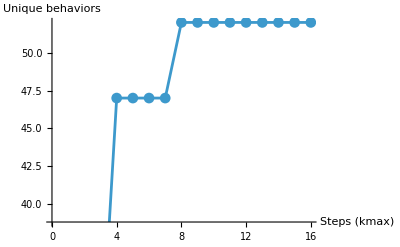

```mathematica
ListLinePlot[uniqueCounts,DataRange->{2,16},PlotMarkers->Automatic,AxesLabel->{"Steps (kmax)","Unique behaviors"}]
```

To identify at which combination of steps and space size real results start to appear, we repeat the previous test also varying the space size, building a results matrix. Red points/regions mark combinations with more than 60 unique behaviors.

```mathematica
spaceSizes=Range[1,8];stepsRange=Range[2,16];resultsMatrix=Table[ecaGraphsS=ParallelTable[MakeGraph[Subscript[i, 2,3],s],{i,0,255,1}];Table[momVecs=ParallelTable[SpectralMoments[g,kmax],{g,ecaGraphsS}];Length[DeleteDuplicates[momVecs]],{kmax,stepsRange}],{s,spaceSizes}]
```

{{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3},{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8},{12,21,21,21,24,24,24,24,24,24,24,24,24,24,24},{29,29,47,47,47,47,52,52,52,52,52,52,52,52,52},{20,22,22,35,36,36,36,36,44,44,44,44,44,49,49},{36,55,56,56,64,64,64,65,65,65,68,68,68,68,68},{25,26,27,28,28,43,43,43,43,43,43,43,56,56,56},{39,40,58,58,59,59,67,67,67,67,67,67,67,67,69}}

```mathematica
ListPlot3D[resultsMatrix,DataRange->{{2,16},{1,8}},AxesLabel->{"Steps","Space size","Unique behaviors"},ColorFunction->(If[#3>60,Red,Blue]&),ColorFunctionScaling->False,Mesh->All]
```

-Graphics3D-

## Functions

## Unprotected functions

```mathematica
Unprotect[RulePlot];

Quiet[RulePlot[CellularAutomaton[{0,1,0}],opts:OptionsPattern[]]=.];
Quiet[RulePlot[CellularAutomaton[{0,1,1/2}],opts:OptionsPattern[]]=.];

RulePlot[CellularAutomaton[{0,1,r_}],opts:OptionsPattern[]]:=Module[{imgSize=Lookup[{opts},ImageSize,100],legend=Lookup[{opts},PlotLegends,None],restOpts=FilterRules[DeleteCases[{opts},(ImageSize|PlotLegends|ColorRules)->_],Options[Graphics]],ref,caseGfx,xCoords,xMin,xMax},ref=RulePlot[CellularAutomaton[{0,2,r}]];
caseGfx=ref[[1,1,1,-1]];
xCoords=Sort@Cases[ref[[1,2]],Line[{{x_,_},{x_,_}}]:>x,Infinity];
xMin=xCoords[[-2]];
xMax=Last[xCoords];
With[{g=Graphics[{caseGfx,{GrayLevel[0.8],{Line[{{xMin,0},{xMin,1}}],Line[{{xMax,0},{xMax,1}}]},{Line[{{xMin,0},{xMax,0}}],Line[{{xMin,1},{xMax,1}}]}}},ImageSize->imgSize,Sequence@@restOpts]},If[legend===None,g,Legended[g,legend]]]];

Protect[RulePlot];
```

SetDelayed::write: Tag RulePlot in RulePlot[CellularAutomaton[{0,1,r_}],opts:OptionsPattern[]] is Protected.

## Plot functions

```mathematica
colorRules[n_:10]:=Join[{0->RGBColor[1., 1., 1.]},Table[k->ColorData["Rainbow"][k/(n)],{k,1,(n)}]];
```

```mathematica
CaRulePlot[ca_Subscript,opts:OptionsPattern[]]:=
RulePlot[CellularAutomaton[{ca[[1]],ca[[2]],(ca[[3]]-1)/2}],opts,ColorRules->colorRules[ca[[2]]-1],opts];
```

```mathematica
rulialGraph[trans_,colorA_:Red,colorB_:Blue,labelA_:"Delete Last State",labelB_:"Minor inverse rule"]:=Module[
{
edges=Join[trans[[1]],trans[[2]]],
edgeStyles=Join[(#->Directive[colorA,Thick])&/@trans[[1]],(#->Directive[colorB,Thick])&/@trans[[2]]],
nodePlot=Function[v,If[v[[2]]<1,Graphics[{GrayLevel[0.9],Rectangle[]},ImageSize->{30,25}],RulePlot[CellularAutomaton[v],ImageSize->{Automatic,30},ColorRules->colorRules]]]
},
Legended[
LayeredGraph[
Graph[
edges,
EdgeStyle->edgeStyles,
VertexShapeFunction->(Inset[Column[{nodePlot[#2],Style[Subscript[#2[[1]],#2[[2]],1],Small,Black]},Alignment->Center],#1]&),
VertexSize->{0.11,100.03}
],
ImageSize->{Automatic,Automatic},
AspectRatio->2],
LineLegend[{colorA,colorB},{labelA,labelB}]
]
]
```

## Functions

```mathematica
getRules[s_,n_]:=ParallelMap[Subscript[#,s,n]&,Range[0,s^(s^n)-1]]
```

```mathematica
CaRulePlot[ca_Subscript,opts:OptionsPattern[]]:=
RulePlot[CellularAutomaton[{ca[[1]],ca[[2]],(ca[[3]]-1)/2}],ColorRules->colorRules[ca[[2]]-1],opts];
```

```mathematica
CaArrayPlot[ca_Subscript,s_,t_,opts:OptionsPattern[]]:=
ArrayPlot[CellularAutomaton[{ca[[1]],ca[[2]],(ca[[3]]-1)/2},s,t],ColorRules->colorRules[ca[[2]]-1],opts];
```

```mathematica
CaArray[ca_Subscript,s_,t_]:=Module[{},
CellularAutomaton[{ca[[1]],ca[[2]],(ca[[3]]-1)/2},s,t]
]
```

### Direct relations

```mathematica
addData[rulesIn_List,dataIn_Association:<||>]:=Module[
{
data=dataIn,rules=rulesIn,
inverseRules,mirrorRules,stateRules,neighborRules,joinRules
},
{inverseRules,mirrorRules,stateRules,neighborRules}=Parallelize[{
DeleteDuplicates@Flatten[Table[Map[rule->#&,InverseRules[rule]],{rule,rules}]],
DeleteDuplicates@Flatten[Table[Map[rule->#&,MirrorRules[rule]],{rule,rules}]],
Select[Map[#->DeleteState[#]&,rules],#[[2]]=!=Null&],
Select[Map[#->DeleteNeighbor[#]&,rules],#[[2]]=!=Null&]
}];

<|
"inverse"->DeleteDuplicates[Join[Lookup[dataIn,"inverse",{}],inverseRules]],
"mirror"->DeleteDuplicates[Join[Lookup[dataIn,"mirror",{}],mirrorRules]],
"state"->DeleteDuplicates[Join[Lookup[dataIn,"state",{}],stateRules]],
"neighbor"->DeleteDuplicates[Join[Lookup[dataIn,"neighbor",{}],neighborRules]]
|>
]
```

```mathematica
reduce[data_]:=Module[{dataUnq},
dataUnq=ReplaceAll[data,ParallelMap[Reverse,data["inverse"]]];
dataUnq=ReplaceAll[dataUnq,ParallelMap[Reverse,dataUnq["mirror"]]];
ParallelMap[DeleteDuplicates,dataUnq[[{"inverse","join","state","neighbor"}]]]
]
```

#### InverseRule

```mathematica
InverseRules[ca_Subscript]:=Module[
{
r=ca[[1]],s=ca[[2]],n=(ca[[3]]-1)/2,
L=ca[[2]]^ca[[3]],outputs,tuples,perms,res
},
outputs=Reverse[IntegerDigits[r,s,L]];(*outputs[[k]]=salida de la vecindad k-1*)
tuples=IntegerDigits[#,s,2n+1]&/@Range[0,L-1];(*tuples[[k]]=vecindad k-1 como n-tupla*)
perms=Permutations[Range[0,s-1]];(*solo s! permutaciones de ESTADOS*)
res=Sort@DeleteDuplicates@Table[
Module[
{pi=AssociationThread[Range[0,s-1]->perm],newOut=ConstantArray[0,L]},
Do[
newOut[[FromDigits[pi/@tuples[[k]],s]+1]]=pi[outputs[[k]]]
,{k,1,L}
];
FromDigits[Reverse[newOut],s]]
,{perm,perms}
];
Subscript[#,ca[[2]],ca[[3]]]&/@res
]
```

#### Mirror Rules

```mathematica
MirrorRules[ca_Subscript]:=Module[{pos,rule,assoc,res},
pos=IntegerDigits[#,ca[[2]],ca[[3]]]&/@Range[0,ca[[2]]^ca[[3]]-1];
rule=IntegerDigits[ca[[1]],ca[[2]],Length[pos]];
assoc=Transpose[{pos,rule}];
res=Sort@DeleteDuplicates[{ca[[1]],FromDigits[
SortBy[{Reverse[#[[1]]],#[[2]]}&/@assoc,#[[1]]&][[;;,2]],
ca[[2]]
]}];
Subscript[#,ca[[2]],ca[[3]]]&/@res
]
```

#### Delete state

```mathematica
DeleteState[ca_Subscript]:=Module[{vector,pos,rule,newpos},If[ca[[2]]==1,Return[];];
vector=IntegerDigits[Range[ca[[2]]^ca[[3]]-1,0,-1],ca[[2]]];
pos=Position[vector,ca[[2]]-1][[;;,1]];
rule=IntegerDigits[ca[[1]],ca[[2]],ca[[2]]^ca[[3]]];
If[rule[[pos]]==ConstantArray[0,Length[pos]]&&Not@ContainsAny[rule,{ca[[2]]-1}],
(*Puede eliminarse ese estado*)
newpos=Complement[Range[ca[[2]]^ca[[3]],1,-1],pos];
Subscript[FromDigits[rule[[newpos]],ca[[2]]-1],ca[[2]]-1,ca[[3]]],
(*No puede eliminarse*)
Null]];
```

#### Delete neighbor

```mathematica
DeleteNeighbor[ca_Subscript]:=Module[
{r,s,n,rv,tuples,ruleIdx,indepQ,ip,relPos,nRed,redRV},
r=ca[[1]];s=ca[[2]];n=ca[[3]];
If[n==1,Return[];];
rv=IntegerDigits[r,s,s^n];
tuples=IntegerDigits[#,s,n]&/@Range[s^n-1,0,-1];
ruleIdx[inp_]:=s^n-FromDigits[inp,s];
indepQ[pos_]:=AllTrue[tuples,Function[inp,SameQ@@Table[rv[[ruleIdx[ReplacePart[inp,pos->v]]]],{v,0,s-1}]]];
ip=Select[Range[n],indepQ];
If[Length[ip]==0,Null,relPos=Complement[Range[n],{ip[[1]]}];(*solo elimina 1 posición*)nRed=n-1;
redRV=rv[[ruleIdx[ReplacePart[ConstantArray[0,n],Thread[relPos->#]]]]]&/@(IntegerDigits[#,s,nRed]&/@Range[s^nRed-1,0,-1]);
Subscript[FromDigits[redRV,s],s,n-1]]]
```

### Graph relations

```mathematica
MakeGraph[ca_Subscript,spaceSize_]:=Module[{inits},
inits=Tuples[Range[0,ca[[2]]-1],spaceSize];
Graph[
Map[
FromDigits[#[[1]],2]->FromDigits[#[[2]],2]&,(CaArray[ca,#,1]&/@inits)],
VertexLabels->Automatic]
]
```

```mathematica
EigenvaluesGraph[g_Graph]:=Eigenvalues[N[Normal[AdjacencyMatrix[g]]]]
```

```mathematica
EigenvaluesGraphDistance[g1_Graph,g2_Graph]:=Module[{ev1,ev2},
ev1=Eigenvalues[N[Normal[AdjacencyMatrix[g1]]]];
ev2=Eigenvalues[N[Normal[AdjacencyMatrix[g2]]]];
CosineDistance[ev1,ev2]
]
```